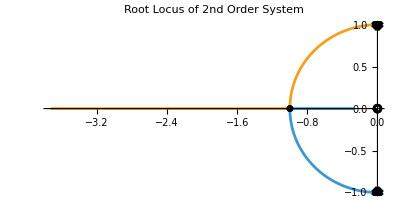

```mathematica
(*定义传递函数，假设 wn=1*)wn=1;
tf=TransferFunctionModel[wn^2/(s^2+2*zeta*wn*s+wn^2),s];

(*绘制根轨迹，观察 zeta 从 0 到 2 的变化*)
RootLocusPlot[tf,{zeta,0,2},PlotLabel->"Root Locus of 2nd Order System",FeedbackType->None]
```

```mathematica
Manipulate[Module[{poles,c1,c2},(*计算极点数值*)poles=s/. Solve[s^2+2*zeta*wn*s+wn^2==0,s];
c1=poles[[1]];
c2=poles[[2]];
ComplexListPlot[{c1,c2},PlotRange->{{-1.5*wn,0.5*wn},{-1.2*wn,1.2*wn}},PlotStyle->Directive[Red,PointSize[Large]],Epilog->{(*修正后的圆弧绘制：样式需放在前面*){Dashed,Gray,Circle[{0,0},wn,{Pi/2,3*Pi/2}]},(*标注极点位置*)Text[Style["c1",12,Bold],{Re[c1],Im[c1]},{-1.5,-1}],Text[Style["c2",12,Bold],{Re[c2],Im[c2]},{-1.5,1}]},AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"Re(s)","Im(s)"},PlotLabel->Row[{"Damping Ratio ",Style["ζ = ",Italic],zeta}]]],{{zeta,0.5,"ζ (Damping Ratio)"},0,2,Appearance->"Labeled"},{{wn,1,"ωn (Natural Frequency)"},0.5,2,Appearance->"Labeled"}]
```